# Embedding Diagram (Titelseite)

```mathematica
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
```

## Rechnungen

Ein Embedding-Diagram kriegt man schlussendlich mit so einer Formel hier:

```mathematica
zV[V_] := Integrate[ √(V[r]/(1-V[r])),r]
```

Das kann man mal testweise anwenden auf:

```mathematica
Schwarzschild = Function[r,(2GM)/r];
zV@Schwarzschild
```

(2 √2 GM)/(√(GM/(-2 GM+r)))

```mathematica
deSitter = Function[r,Λ/3 r^2];
deSitterCore = Function[r,2GM r^2];
zV@deSitter
```

-(√((r^2 Λ)/(3-r^2 Λ)) (3-r^2 Λ))/(r Λ)

Geplottet sieht das schon ganz gut aus:

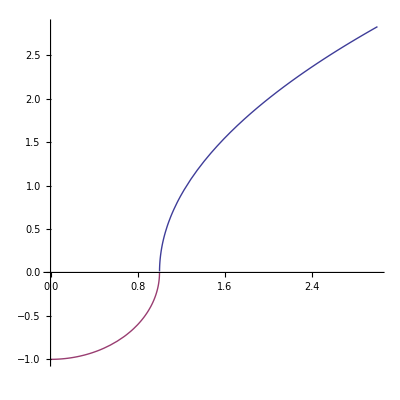

```mathematica
Plot[
zV/@Thread@Function[r,{1/r, r^2}] // Evaluate,
{r,0,3},
AspectRatio->1
]
```

```mathematica
(* Abschnittsweise definieren *)
embeddF[r_] =zV@Function[r,If[r≥  1,1/r,r^2]]
```

Piecewise[{{-r/(√(-r^2/(-1+r^2))), r≤1}, {2/(√(1/(-1+r))), True}}]

```mathematica
embeddF[3]
```

2 √2

### Numerisch bestimmt für hα

```mathematica
hα[r_,α_] = r^3 / (r^α + 1/2)^(3/α);
Vregular[α_] := Function[r,hα[r,α] / r];
```

```mathematica
(* Fuer ein paar Alpha geht das analytisch, fuer andere nicht *)
zV@Vregular[α]
zV@Vregular@5(* geht zb mit α->2 *)
```

∫√((r^2 (1/2+r^α)^(-3/α))/(1-r^2 (1/2+r^α)^(-3/α)))ⅆr

∫√(r^2/((1/2+r^5)^(3/5) (1-r^2/((1/2+r^5)^(3/5)))))ⅆr

```mathematica
(* numerische Integration *)
zVN[V_,x_]:= NIntegrate[ √(V[r]/(1-V[r])),{r,0,x}]
(* Adaptive Wertetabelle, Algo von CompletenessPlot (GUP) *)
dataTable[f_, Xmin_, Xmax_] := Module[{data},
(* Erzeuge adaptive Wertetabelle *)
data=Reap[Plot[f[x],{x,Xmin,Xmax},EvaluationMonitor:>Sow@{x,f[x]}]]⟦-1,1⟧;
(* Sortiere sie nach steigenenden x-Werten *)
data = Sort[data,#1⟦1⟧ < #2⟦1⟧ &];
(* return *) data
]
```

```mathematica
vregdata=dataTable[zVN[Vregular@2,#]&, 0,10];
regprofile=Function[r,Interpolation[vregdata][r]]
```

Function[r,Interpolation[vregdata][r]]

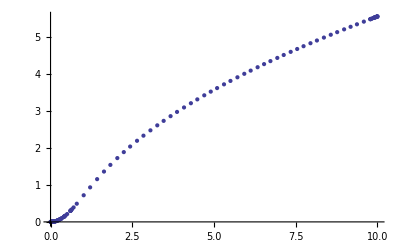
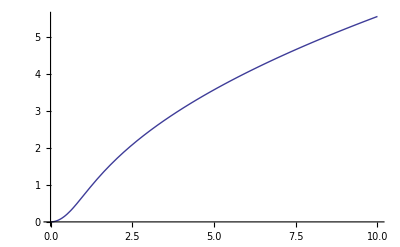

```mathematica
(* Das klappt jetzt super: *)
{ListPlot[vregdata], Plot[regprofile[r],{r,0,10}]}
```

```mathematica
(* Profil noch korrekt verschieben *)
embedRegular = Function[r, regprofile[r]-regprofile[1]];
```

## 3d-Plot

```mathematica
(* maximales r bzw eher maximales x, y *)
rM=3;
(* Einsichtswinkel und abgerundete Ecken *)
clipRange =(* Not[x≥ 0 ∧ y≤0]*)
-π≤ ArcTan[x,y] ≤π∧ Norm[{x,y},3] ≤ rM;
(* Boundary Style *)
boundstyle= {Thick, GrayLevel[0.4]};

p1=Plot3D[With[{r=Norm[{x,y}]},{
2/(√(1/(-1+r)))
}
],{x,-rM,rM},{y,-rM,rM},Mesh->Automatic,MeshStyle->LightGray,
PlotStyle-> {{Green,Opacity[0.5]}, {Red,Opacity[0.1]}},
ImageSize-> Large,
RegionFunction-> Function[{x,y,z}, clipRange],
PlotRange-> {-2,3.5},
Boxed-> False, Axes->False,PlotRangePadding->0,
ColorFunction-> "LakeColors",
ViewAngle-> .41,
BoundaryStyle->boundstyle,
ClippingStyle-> None
(*MeshFunctions -> {Norm[{#1,#2}]&, #2&}*)(*klappt nicht richtig*)
]
```

-Graphics3D-

```mathematica
p2=Plot3D[With[{r=Norm[{x,y}]},
-r/(√(-r^2/(-1+r^2)))*2
],{x,-rM,rM},{y,-rM,rM},Mesh->Automatic,MeshStyle->LightGray,
PlotStyle-> {Opacity[0.5], {Red,Opacity[0.1]}},
ImageSize-> Large,
RegionFunction-> Function[{x,y,z},clipRange ∧ Norm[{x,y}]≤ 1],
PlotRange-> {-4,0},
Boxed-> False, Axes->False,
ColorFunction-> "SolarColors",
BoundaryStyle->boundstyle
(*MeshFunctions -> {Norm[{#1,#2}]&, #2&}*)(*klappt nicht richtig*)
]
```

-Graphics3D-

```mathematica
myDisk[{x_,y_,z_},r_]:=Polygon@Table[{x,y,z}+r {Cos[ϕ],Sin[ϕ],0}//N,{ϕ,0,2 π,2 π/200}]
disk =Graphics3D[{Opacity[0],Red, EdgeForm@{Thick,Red,Opacity[0.5]},myDisk[{0,0,0},1]}];

fig=Show[p1,p2]
```

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{BoxRatios→{1,1,0.4},Boxed→False,ImageSize→{576.,576.},Lighting→Neutral,Method→{RotationControl→Globe},PlotRange→{{-3,3},{-3,3},{-2,3.5}},PlotRangePadding→0,ViewAngle→0.41,ViewPoint→{-1.17974,3.10305,0.655216},ViewVertical→{0.,0.,1.}}

```mathematica
fig=Show[fig,ViewPoint->{-1.1797418825755535,3.103047014541739,0.6552162360935874},ViewVertical->{0.,0.,1.}]
```

-Graphics3D-

```mathematica
figPX=ImageCrop@Rasterize[fig, ImageSize-> 40cm]
Export["../figures/titlepage-3d.png", Show@figPX]
```

-Graphics-

../figures/titlepage-3d.png

## Plot zur Erläuterung auf der zweiten Seite

Hier im Stile der titlepage-3d.nb ein Erläuterungsplot, der das ganze erklärt.

Und: Ja, im obigen Plot ist ein bisschen gecheatet, damit er besser aussiehtl.

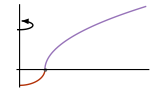

```mathematica
(* Circle replacement with arrows *)
circle[o_,r_,{a_,b_}, res_:100]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
fig=Show[MapThread[
Function[{func, colorfunc},
Plot[Evaluate[func],{r,0,5}, PlotRange-> {-1,4},
Ticks->None,
AxesStyle->Directive@{Opacity[0.5],Gray,Arrowheads[{0.0,0.03}]},
ImageSize-> 5.5cm,
(*Epilog-> {
Red,
Line@{{0,0},{1,0}},
Black,
Arrowheads[{0.0,0.03}],
circle[{0,2.8}, 0.35 {1.5,0.8}, {0,1.7}π+3/4π]
},*)
PlotRangeClipping->False,
PlotRangePadding->0.6,
ColorFunction-> colorfunc
]
],{{-r/(√(-r^2/(-1+r^2))),2/(√(1/(-1+r)))},
{
(* The colors from the 3d plot *)
"SolarColors",
(Blend[RGBColor/@({75,14,135}/#&/@{255,10}),#1]&)
(*"LakeColors"*)
} }],
Graphics@{
(*Red,
Line@{{0,0},{1,0}},*)
Black,
Arrowheads[{0.0,0.03}],
circle[{0,2.8}, 0.35 {1.5,0.8}, {0,1.7}π+3/4π],
Thick, GrayLevel[0.4],
Disk[{1,0},{1,1.618}0.07]
}
]
```

```mathematica
Export["../figures/titlepage-explain.pdf", fig]
```

../figures/titlepage-explain.pdf